# Deflection by Magentic field

```mathematica
mp=938.272;
c=299.792458;
B=0.064;
r=0.11;
T=250;
T1[α_]:=T Cos[α/2]^2
P1[α_]:={ √(T (2 mp+T))Cos[α/2]^2,(√(mp T) Sin[α])/(√2)}
θ1[α_]:=ArcTan[√(T (2 mp+T)) Cos[α/2]^2,(√(mp T) Sin[α])/(√2)]
Rot1[θ_]:={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
T2β[T_]:=(√(2 mp T+T^2))/(mp +T)
Bρ[α_]:=T2β[T1[α]]/(√(1-T2β[T1[α]]^2))mp/c;
ρ[α_]:=Bρ[α]/B;
Δθ[α_]:=r/ρ[α];
```

```mathematica
T2β[T1[40°]]
1/(√(1-%^2))
Δθ[40°]
```

0.587073

1.23528

0.00310175

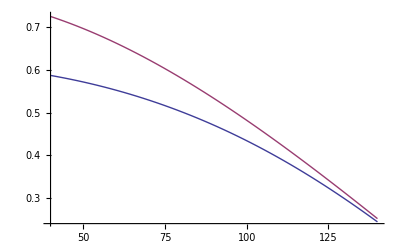

```mathematica
Plot[{T2β[T1[α °]],T2β[T1[α °]]/(√(1-T2β[T1[α °]]^2))},{α,40,140}]
```

```mathematica
Manipulate[Graphics[{
Arrow[{{0,0},{1.400,0}}],
Arrow[{{0,0},p1=1.02237{Cos[π/3],Sin[π/3]}}],
Arrow[{{0,0},p2=1.4{Cos[π/3],Sin[π/3]}}],
Line[{p1-0.170{Sin[π/3],-Cos[π/3]},p1+0.950{Sin[π/3],-Cos[π/3]}}],
Line[{p2-0.3{Sin[π/3],-Cos[π/3]},p2+1.3{Sin[π/3],-Cos[π/3]}}],
Circle[{0,0},r],
Arrow[{{0,0},1.6 Normalize[P1[α °]]}],
{Red,PointSize[Large],Point[1.02237/Cos[π/3-θ1[α °]] Normalize[P1[α °]]]},
Text[1.02237/Cos[π/3-θ1[α °]] Sin[π/3-θ1[α °]],{0.9,0.100}],
Line[{{0,0},(p0=ρ[α °]Rot1[π/2].Normalize[P1[α °]])0.01}],
Blue,
Arrow[{{0,0},2 Rot1[Δθ[α °]].Normalize[P1[α °]]}],
Red,Rotate[Circle[p0,Norm[p0],{0,Δθ[α °]}],θ1[α °]-π/2,p0]
},PlotRange->{{-0.1, 2},{-0.1,1.5}},ImageSize->600],{α,40, 140}]
```

```mathematica
Manipulate[Graphics[{
Circle[{0,0},r],
Arrow[{{0,0},{0.2,0}}],
Line[{{0,0},{0,j},p={0,j}-Rot1[2ArcSin[r/(2j)]].{0,j}}],
Circle[{0,j},j],
Arrow[{p-Rot1[2ArcSin[r/(2j)]].{0.2,0},p+Rot1[2ArcSin[r/(2j)]].{0.2,0}}],
Arrow[{{r/2,0},{ r/2,0}+Rot1[2ArcSin[r/(2j)]].{0.2,0}}]
}],{j,0.1,1}]
```

```mathematica
Series[ArcSin[x],{x,0,10}]
```

x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152+O[x]^11

```mathematica
Series[Sin[2ArcSin[x]],{x,0,10}]
```

2 x-x^3-x^5/4-x^7/8-(5 x^9)/64+O[x]^11

```mathematica
Ay={0.3233,0.1586,-0.03654,-0.2207,-0.3545};
P[i_,a_,b_]:=1/Ay[[i]] (a-b)/(a+b)
ΔP[i_,a_,b_]:=1/(2 Ay[[i]]) √((a b)/(a+b)^3)
```

```mathematica
Needs["ErrorBarPlots`"]
```

{-0.41843,0.0381207,0.204889,-0.168859,-0.386617}

{0.0394596,0.0548121,-0.223745,-0.044606,-0.0497706}

{{-0.41843,0.0394596},{0.0381207,0.0548121},{0.204889,-0.223745},{-0.168859,-0.044606},{-0.386617,-0.0497706}}

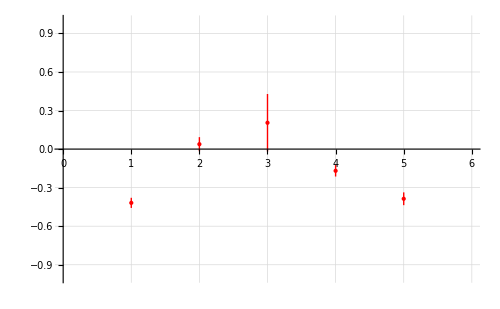

```mathematica
NL1={163,416,464,334,112};
NR1={214,411,471,310,85};
Plist=Table[P[i,NL1[[i]],NR1[[i]]],{i,1,5}]
ΔPlist=Table[ΔP[i,NL1[[i]],NR1[[i]]],{i,1,5}]
Table[{Plist[[i]],ΔPlist[[i]]},{i,1,5}]
ErrorListPlot[%,PlotRange->{{0,6},{-1,1}},PlotStyle->Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500]
```

{-0.506473,-0.0956647,-0.760202,-0.0974417,-0.501489}

{0.0412496,0.0585353,-0.24302,-0.0479424,-0.0517266}

{{-0.506473,0.0412496},{-0.0956647,0.0585353},{-0.760202,-0.24302},{-0.0974417,-0.0479424},{-0.501489,-0.0517266}}

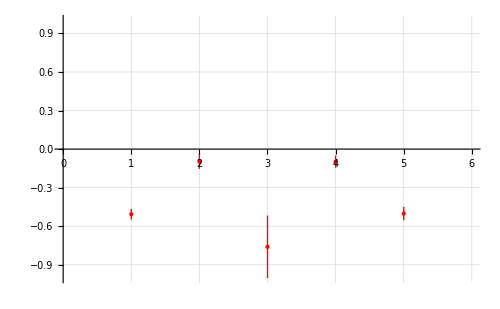

```mathematica
NL2={143,357,407,285,106};
NR2={199,368,385,273,74};
Plist=Table[P[i,NL2[[i]],NR2[[i]]],{i,1,5}]
ΔPlist=Table[ΔP[i,NL2[[i]],NR2[[i]]],{i,1,5}]
Table[{Plist[[i]],ΔPlist[[i]]},{i,1,5}]
ErrorListPlot[%,PlotRange->{{0,6},{-1,1}},PlotStyle->Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500]
```

{0.045028,0.0668941,0.482595,-0.0357393,0.0588958}

{0.0410347,0.056644,-0.233201,-0.0462741,-0.0517035}

{{0.045028,0.0410347},{0.0668941,0.056644},{0.482595,-0.233201},{-0.0357393,-0.0462741},{0.0588958,-0.0517035}}

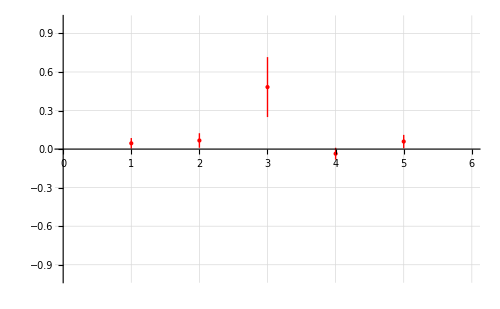

```mathematica
NL=Table[√(NL1[[i]]NR2[[i]]),{i,1,5}];
NR=Table[√(NL2[[i]]NR1[[i]]),{i,1,5}];
Plist=Table[P[i,NL[[i]],NR[[i]]],{i,1,5}]
ΔPlist=Table[ΔP[i,NL[[i]],NR[[i]]],{i,1,5}]
Table[{Plist[[i]],ΔPlist[[i]]},{i,1,5}]
ErrorListPlot[%,PlotRange->{{0,6},{-1,1}},PlotStyle->Red,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500]
```